# Report Project 1

Course code: IX1500
Date: 2017-09-13

Evan Saboo, name1@kth.se
Xing Guan, xguan@kth.se

Task 1a: Poker Probability by census method

## Summery

### Task

The first task is to calculate the exact probability of the following hands in a variation of a poker game:

one pair

two pairs

three of a kind

four of a kind

five of a kind

full hand

straight

flush

straight flush

nothing

To calculate the exact probability  we will be using the census method.
The poker game consists of the cards 8,9,10,J,Q,K,A from two decks to construct sets of five playing cards. If one of the hand does contain more than one rank then the highest rank is considered e.g. if we want to calculate the probability of three of a kind and one of hands contains one pair, two pairs, three of a kind and full hand then the highest rank (full hand) is considered and it will be excluded from the calculation.

### Result

Hand | Probability | Probability,%
One pair | 11920/22737 | 0,5242556186
Two pair | 870/7579 | 0,1147908695
Three of a kind | 2240/22737 | 0,09851783437
Four of a kind | 140/22737 | 0,006157364648
Five of a kind | 7/68211 | 0,0001026227441
Full hand | 392/22737 | 0,01724062101
Straight | 1360/53053 | 0,02563474262
Flush | 953/477477 | 0,001995907656
Straight flush | 16/159159 | 0,0001005284024
Nothing | 0 | □

## Calculating poker Probability by census method

### A pair

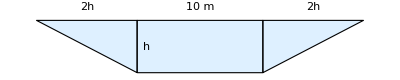

The given trapezoid area is

a(h)=(10+2h)h

0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

The data is interpolated as a function A(x).

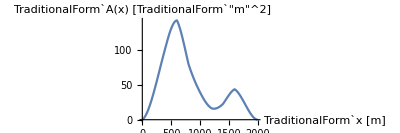

### Two pairs

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Code

Task 1b: Poker Probability by combinatorial calculus

```mathematica
Kopiera in allt
```

## Summery

### Task

The second task is to use combinatorial calculus to calculate the probability of flush, straight, full house, 3 of a kind and 4 of a kind. Every rank has to be compared to task 1a to check if the answers match.

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

Hand | Probability | Probability,%
Flush | □ | □
Straight | □ | □
Full house | □ | □
Three of a kind | □ | □

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

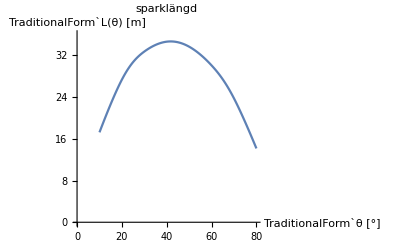

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

```mathematica
ClearAll["`*"]
```

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```

Task 1c: Poker Probability by Monte Carlo method

## Summery

### Task

In the last task we are going to calculate the probability of getting one pair using the Monte Carlo method. We will also draw a diagram that shows how the probability estimate stabilises with increasing sample size. This task will also be compared to task 1a to check if our approximate answer is close to the exact answer.

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

-Graphics-

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

```mathematica
ClearAll["`*"]
```

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```